# TT Term Reference Value : J/psi,5.02 TeV (0.725, 0.005136863) (2.15,0.002442843)

## v_T=0.25,γ_c=0.39,m_c=1.28(fixed),T=0.19(0.16-0.19)

```mathematica
TT[p_,eta_,gamc_]:=36*Sqrt[p^2+3.096^2]*(5*5.0676896*Pi(9*5.0676896)^2)/(2Pi)^3*2*gamc^2*BesselI[0,(p Sinh[eta])/0.19]*BesselK[1,Cosh[eta]/0.19(Sqrt[1.28^2+0.25 p^2]+Sqrt[1.28^2+0.25 p^2])];
```

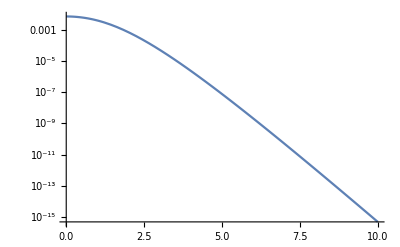

```mathematica
LogPlot[TT[p,ArcTanh[0.25],0.39],{p,0,10}]
```

```mathematica
(*(0.725,0.005136863) (2.15,0.002442843)*)
```

```mathematica
TT[0.725,ArcTanh[0.25],0.39]
TT[2.15,ArcTanh[0.25],0.39]
```

0.00517196

0.000485625

```mathematica
ArcTanh[0.25]
```

0.255413

## Thermal improve TS: T 0.185->0.175

```mathematica
Thermal[p_,eta_]:=BesselI[0,(p Sinh[eta])/0.185]*BesselK[1,(Sqrt[1.28^2+p^2]Cosh[eta])/0.185]*Sqrt[1.28^2+p^2]
```

```mathematica
Thermal[2.15/2,0.28]
```

0.000106819

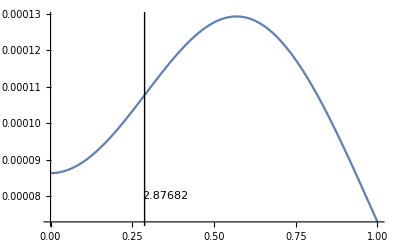

```mathematica
Plot[{Thermal[2.15/2,eta]},{eta,0,1},Epilog->{Line[{{0.287682,0},{0.287682,1}}],Inset[Framed[Style["2.87682",10],Background->LightYellow],{0.35,0.00008}]}]
```